# Signals & Systems Winter 1400 Intro to Mathematica Prepared by : Shayan Vassef , Email : sh.vassef@ut.ac.ir Table of contents

The very basics

2D and 3D Graphics

Creating Interactive Models

Algebraic Manipulation and Equation
Solving

Calculus

Differential Equations

## The very basics

### Basic Operations

```mathematica
2+2
```

4

```mathematica
580/13
```

580/13

```mathematica
N[580/13]
```

44.6154

```mathematica
580/13//N
```

44.6154

```mathematica
N[580/13,3]
```

44.6

WolframAlphaQueryResults

```mathematica
580/13
```

### Variable Assignments

```mathematica
x=5
```

5

```mathematica
3*x+2
```

17

```mathematica
Clear[x]
```

```mathematica
x
```

x

## 2D and 3D Graphics

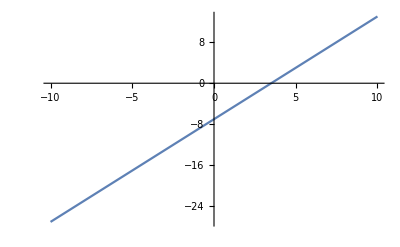

```mathematica
Plot[2 x-7,{x,-10,10}]
```

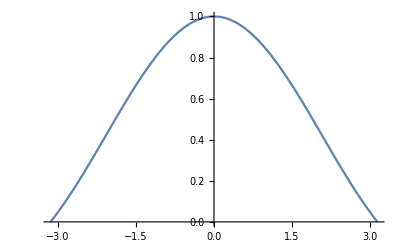

```mathematica
Plot[Sin[x]/x,{x,-Pi,Pi}]
```

WolframAlphaQueryParseResults

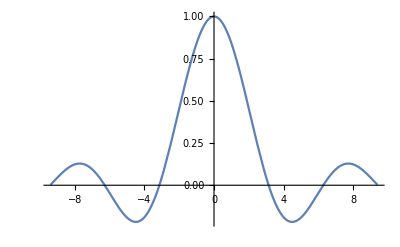

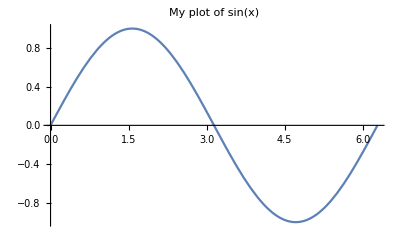

```mathematica
Plot[Sin[x],{x,0,2 π},PlotLabel->    "My plot of sin(x)"]
```

```mathematica
Plot[Sin[x],{x,0,2 π},PlotLabel-> "My plot of "<>"sin(x)"]
```

-Graphics-

```mathematica
Plot3D[Sin[x*y],{x,-3,3},{y,-5,5}]
```

-Graphics3D-

WolframAlphaQueryParseResults

-Graphics3D-

```mathematica
?Plot*
```

WolframAlphaQueryParseResults

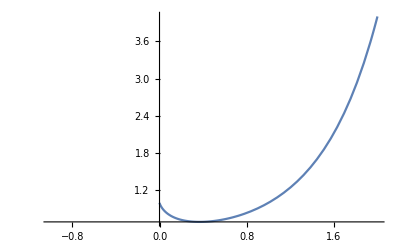

WolframAlphaQueryParseResults

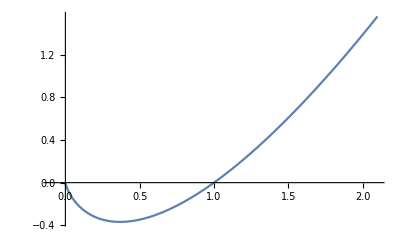

WolframAlphaQueryParseResults

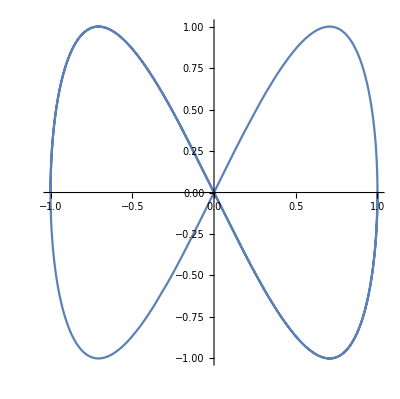

WolframAlphaQueryParseResults

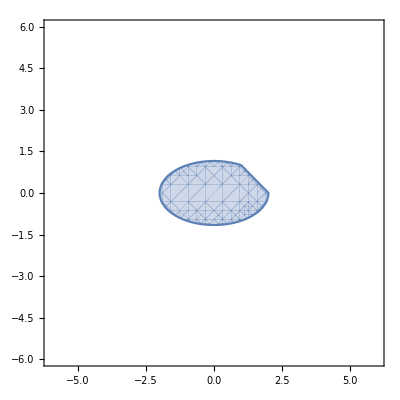

### Plotting Multiple Functions Together

WolframAlphaQueryParseResults

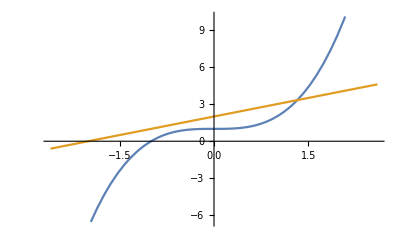

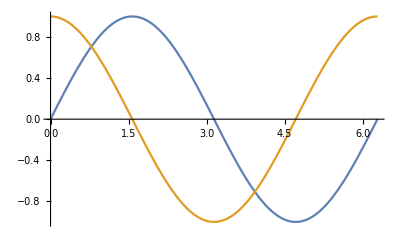

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 π}]
```

### Defining functions

```mathematica
f[x_]:=x^2
f[2]
```

4

```mathematica
f[{1,2,3}]
```

{1,4,9}

```mathematica
Clear[a,b]
```

```mathematica
h[a_,b_]:=a*b

h[10,10]
```

100

```mathematica
Clear[x,a,f,h]

h[x_]=Piecewise[{{2x, x<0}, {x^2, 0≤x<2}, {2+x, x>2}}]
```

Piecewise[{{2 x, x<0}, {x^2, 0≤x<2}, {2+x, x>2}, {0, True}}]

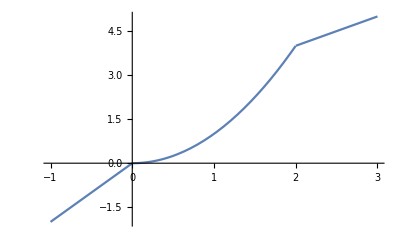

```mathematica
Plot[h[x],{x,-1,3}]
```

#### Using Options with Graphics

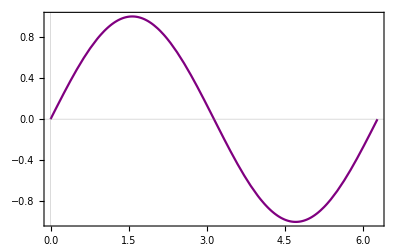

```mathematica
Plot[Sin[x],{x,0,2 π},PlotTheme-> "Scientific",PlotStyle-> Purple]
```

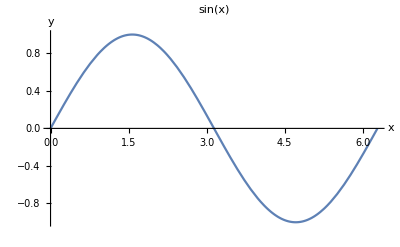

```mathematica
Plot[Sin[x],{x,0,2 π},PlotLabel-> Style["sin(x)",FontSize-> 14,FontFamily-> "Arial",FontColor-> Blue],AxesLabel-> {Style["x",FontSize-> 14,Bold],Style["y",FontSize->14,Bold]}]
```

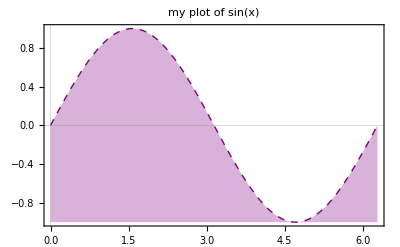

```mathematica
Plot[Sin[x],{x,0,2 π},PlotTheme-> "Scientific",PlotStyle-> {Purple,Thick,Dashed},Filling-> Bottom,PlotLabel-> "my plot of sin(x)"]
```

WolframAlphaQueryParseResults

WolframAlphaQueryParseResults

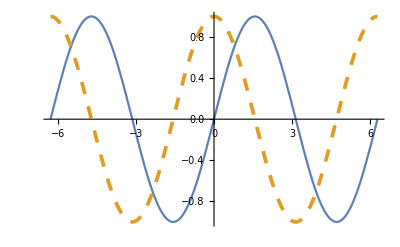

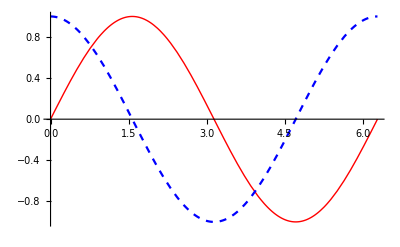

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 π},PlotStyle-> {{Red,Thick},{Blue,Dashed}}]
```

### Ticks

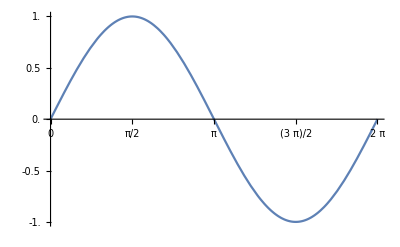

```mathematica
Plot[Sin[x],{x,0,2 π},Ticks-> {Range[0,2 π,π/4],Range[-1,1,0.25]}]
```

### PlotLegends

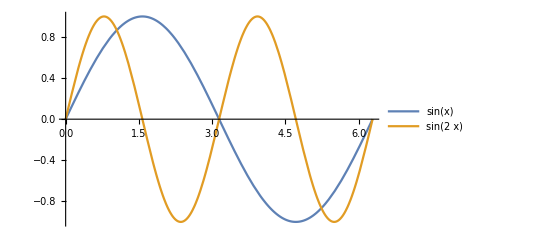

```mathematica
Plot[{Sin[x],Sin[2 x]},{x,0,2 π},PlotLegends-> "Expressions"]
```

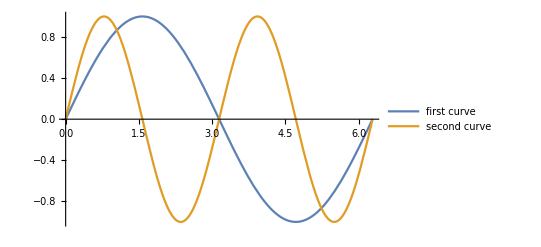

```mathematica
Plot[{Sin[x],Sin[2 x]},{x,0,2 π},PlotLegends-> {"first curve","second curve"}]
```

```mathematica
myPlot[eq1_,eq2_]:=
Plot[{eq1,eq2},{x,0,2 π},
PlotStyle-> {Directive[Red,Thick],Directive[Gray,Thick,Dashed]},
PlotLegends-> Placed["Expressions",Above]]
```

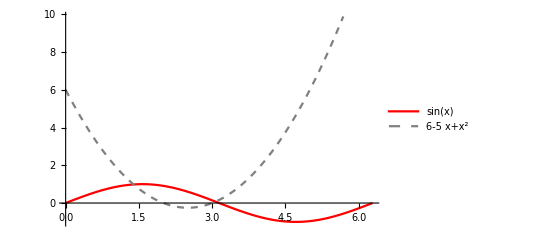

```mathematica
myPlot[Sin[x],x^2-5*x+6]
```

## Creating Interactive Models



```mathematica
Plot[Sin[x],{x,0,2 π}]
```

The goal may be to compare the curve of sin(x) with the curve of sin(2 x), the curve of
sin(3 x), and so on.
To begin, it is important to know that using Manipulate requires three components:

Manipulate command

Expression to manipulate by changing certain parameters

Parameter specifications

Manipulate[
 expression to manipulate,
 parameter specifications]

```mathematica
Manipulate[Plot[Sin[frequency*x],{x,0,2 π}],{frequency,1,5}]
```

```mathematica
Manipulate[Plot[Sin[frequency*x+phase],{x,0,2 π}],{frequency,1,5},{phase,1,10}]
```

```mathematica
Manipulate[Plot[function[frequency*x+phase],{x,0,2 π}],{frequency,1,5},{phase,1,10},{function,{Sin,Cos,Tan,Csc,Sec,Cot}}]
```

The Manipulate command is not restricted to graphical manipulation and can be used with
any Mathematica expression.

```mathematica
Manipulate[Expand[(a+b)^n],{n,2,10,1}]
```

```mathematica
Manipulate[Plot3D[Sin[a x y],{x,-2,2},{y,-2,2}],{a,1,5}]
```

```mathematica
Manipulate[Plot[Sin[f*x],{x,0,2 π},PlotLabel-> "sin("<>ToString[f]<>"x)"],{{f,1,"frequency"},1,5,Appearance-> "Labeled"}]
```

```mathematica
f[x_]:=2*x^2+2*x+1
```

```mathematica
Manipulate[Plot[f[a*x],{x,-4,4},PlotRange-> {0,25}],{a,-1,1}]
```

## Algebraic Manipulation and Equation Solving

```mathematica
2 a b /(b c)
```

(2 a)/c

```mathematica
(a+b) (a+c) (b+c)
```

(a+b) (a+c) (b+c)

```mathematica
Expand[(a+b) (a+c) (b+c)]
```

a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2

```mathematica
Factor[a^2 b+a b^2+a^2 c+2 a b c+b^2 c+a c^2+b c^2]
```

(a+b) (a+c) (b+c)

```mathematica
Together[1/(x-1)+1/(x+1)]
```

(2 x)/((-1+x) (1+x))

```mathematica
Apart[(2 x)/((x-1) (x+1))]
```

1/(-1+x)+1/(1+x)

```mathematica
Collect[a^2 y+2 a b y+b^2 y+2 a x y+2 b x y+x^2 y+c^2 x^2 y+2 c d x^2 y+d^2 x^2 y,{x,y}]
```

(a^2+2 a b+b^2) y+(2 a+2 b) x y+(1+c^2+2 c d+d^2) x^2 y

```mathematica
Simplify[Sin[x]^2+Cos[x]^2]
```

1

```mathematica
FullSimplify[a^2+2 a b+b^2 y+(2 a+2 b) x y+1+c^2+2 c d+d^2 x^2 y]
```

1+(a)^2+2 a b+c^2+2 c d+2 (a+b) x y+ (b^2+d^2 x^2) y

```mathematica
Simplify[(x^2)^0.5]
```

(x^2)^0.5

```mathematica
Simplify[(x^2)^0.5,x>0]
```

x^1.

```mathematica
TrigExpand[Sin[x^2]*Cos[2 x]]
```

Cos[x]^2 Sin[x^2]-Sin[x]^2 Sin[x^2]

### Basic Equation Solving

```mathematica
Solve[x^2+2 x-1==0,x]
```

{{x→-1-√2},{x→-1+√2}}

```mathematica
Solve[{2 x+y == 12,x+4 y == 34},{x,y}]
```

{{x→2,y→8}}

```mathematica
ReplaceAll[{x,x+1,x+2},x-> 2]
```

{2,3,4}

```mathematica
x/.x-> y^2 (* replace all*)
```

y^2

```mathematica
Solve[x^2+2 x-1 == 0,x]
```

{{x→-1-√2},{x→-1+√2}}

```mathematica
(x+3)/.Solve[x^2+2 x-1 == 0,x]
```

{2-√2,2+√2}

### Other Commands for Solving Equations

```mathematica
Solve[x^2-y^3 == 1,{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→-√(1+y^3)},{x→√(1+y^3)}}

```mathematica
Reduce[x^2-y^3 == 1,{x,y}]
```

y==(-1+x^2)^(1/3)||y==-(-1)^(1/3) (-1+x^2)^(1/3)||y==(-1)^(2/3) (-1+x^2)^(1/3)

```mathematica
FindRoot[Sin[x^2]-Cos[x]==0,{x,π}]
```

{x→3.29304}

```mathematica
Reduce[Sin[x^2]-Cos[x] == 0,x]
```

C[1]∈ℤ&&(x==1/2 (-1-√(1+2 π-16 π C[1]))||x==1/2 (-1+√(1+2 π-16 π C[1]))||x==1/2 (-1-√(1+2 π-8 (π+2 π C[1])))||x==1/2 (-1+√(1+2 π-8 (π+2 π C[1])))||x==1/2 (1-√(1+2 π-16 π C[1]))||x==1/2 (1+√(1+2 π-16 π C[1]))||x==1/2 (1-√(1+2 π-8 (π+2 π C[1])))||x==1/2 (1+√(1+2 π-8 (π+2 π C[1]))))

## Calculus

### Differentiation

```mathematica
D[x^2 Sin[x],x]
```

x^2 Cos[x]+2 x Sin[x]

```mathematica
D[x^2 Sin[x],{x,3}]
```

6 Cos[x]-x^2 Cos[x]-6 x Sin[x]

```mathematica
Sin'[x]
```

Cos[x]

```mathematica
f[x_]:=x^3-2 x^2-5 x+6
```

```mathematica
f'[x]
```

-5-4 x+3 x^2

```mathematica
{D[f[x],x],f'[x]} (*equivalant*)
```

{-5-4 x+3 x^2,-5-4 x+3 x^2}

```mathematica
Table[{x,f[x],f'[x],f''[x]},{x,1,10}]//TableForm
```

1 | 0 | -6 | 2
2 | -4 | -1 | 8
3 | 0 | 10 | 14
4 | 18 | 27 | 20
5 | 56 | 50 | 26
6 | 120 | 79 | 32
7 | 216 | 114 | 38
8 | 350 | 155 | 44
9 | 528 | 202 | 50
10 | 756 | 255 | 56

```mathematica
D[x^2 Cos[x y]+y^2 Sin[x y],x,y]
```

-x^3 y Cos[x y]+3 y^2 Cos[x y]-3 x^2 Sin[x y]-x y^3 Sin[x y]

```mathematica
D[Sin[x]^10,{x,4}]
```

5040 Cos[x]^4 Sin[x]^6-4680 Cos[x]^2 Sin[x]^8+280 Sin[x]^10

```mathematica
Simplify[%]
```

10 (141+238 Cos[2 x]+125 Cos[4 x]) Sin[x]^6

```mathematica
D[x g[x],x]
```

g[x]+x g'[x]

```mathematica
D[x g[x],{x,2}]
```

2 g'[x]+x g''[x]

```mathematica
D[g[x^2] g''[x],x]/.g-> Sin
```

-2 x Cos[x^2] Sin[x]-Cos[x] Sin[x^2]

### Limits

```mathematica
Limit[1/x,x-> 1]
```

1

```mathematica
Limit[1/x,x-> Infinity]
```

0

#### Direction

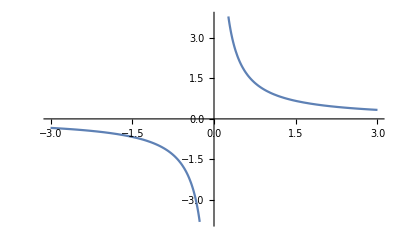

```mathematica
Plot[1/x,{x,-3,3}]
```

```mathematica
Limit[1/x,x->0,Direction->+1](*left*)
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1](*right*)
```

∞

```mathematica
Limit[1/x,x->0](*default direction*)
```

Indeterminate

```mathematica
Limit[x^a,a-> ∞]
```

ConditionalExpression[∞,Log[x]>0]

```mathematica
Limit[x^a,a-> ∞,Assumptions->x>1]
```

∞

```mathematica
Limit[x^a,a-> ∞,Assumptions->x==1]
```

1

### Integration

#### Indefinite Integration

```mathematica
Integrate[x^2+2 x+1,x]
```

x+x^2+x^3/3

```mathematica
∫(x^2+2 x+1)ⅆx
```

x+x^2+x^3/3

WolframAlphaQueryParseResults

-1/2 Cos[x]^2

#### Definite Integration

```mathematica
Integrate[x^2 Exp[x],{x,0,1}]
```

-2+ⅇ

```mathematica
N[%]
```

0.718282

```mathematica
Integrate[x^2 Exp[x],{x,a,b}]
```

-(2+(-2+a) a) ⅇ^a+(2+(-2+b) b) ⅇ^b

```mathematica
Manipulate[
Integrate[x^2 Exp[x],{x,0,a}],
{a,0,8}]
```

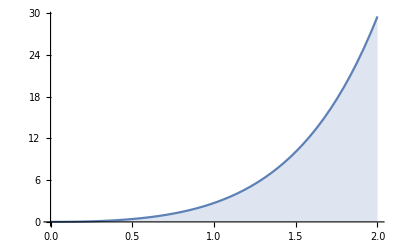

```mathematica
Plot[x^2 Exp[x],{x,0,2},Filling-> Axis]
```

```mathematica
Integrate[x^3 Sin[y]+y^2 Cos[x^2],{x,-1,1},{y,-2,x}]
```

8/3 √(2 π) FresnelC[√(2/π)]

## Differential Equations

### Solving Symbolically with DSolve

```mathematica
DSolve[y'[x] == x^2 Sin[x],y[x],x]
```

{{y[x]→C[1]-(-2+x^2) Cos[x]+2 x Sin[x]}}

```mathematica
DSolve[{y'[x] == x^2 Sin[x],y[1]==1},y[x],x]
```

{{y[x]→1-Cos[1]+2 Cos[x]-x^2 Cos[x]-2 Sin[1]+2 x Sin[x]}}

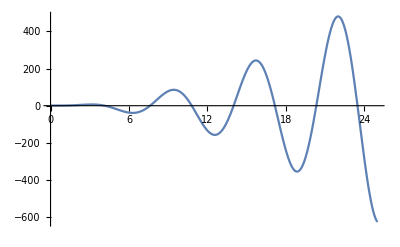

```mathematica
soln=DSolveValue[{y'[x] == x^2 Sin[x],y[1] == 1},y[x],x];
Plot[soln,{x,0,25}]
```

```mathematica
soln=DSolveValue[{y''[x]+y'[x]+y[x] == 0},y[x],x]
```

ⅇ^(-x/2) C[2] Cos[(√3 x)/2]+ⅇ^(-x/2) C[1] Sin[(√3 x)/2]

```mathematica
solnTable=Table[soln/.{C[1]-> i,C[2]-> j},{i,-1,1,1},{j,-1,1,1}](*TableForm*)
```

{{-ⅇ^(-x/2) Cos[(√3 x)/2]-ⅇ^(-x/2) Sin[(√3 x)/2],-ⅇ^(-x/2) Sin[(√3 x)/2],ⅇ^(-x/2) Cos[(√3 x)/2]-ⅇ^(-x/2) Sin[(√3 x)/2]},{-ⅇ^(-x/2) Cos[(√3 x)/2],0,ⅇ^(-x/2) Cos[(√3 x)/2]},{-ⅇ^(-x/2) Cos[(√3 x)/2]+ⅇ^(-x/2) Sin[(√3 x)/2],ⅇ^(-x/2) Sin[(√3 x)/2],ⅇ^(-x/2) Cos[(√3 x)/2]+ⅇ^(-x/2) Sin[(√3 x)/2]}}

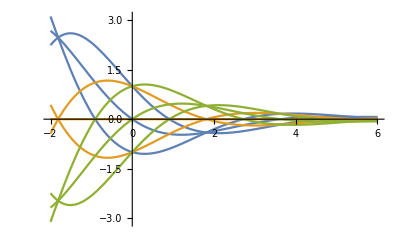

```mathematica
Plot[solnTable,{x,-2,6},PlotRange-> All]
```

### Solving Numerically with NDSolve

```mathematica
NDSolveValue[{y'[x] == x^2 Sin[x],y[1]==1},y,{x,0,10}]
```

InterpolatingFunction[…]

```mathematica
res=NDSolveValue[{y'[x] == x^2 Sin[x],y[1]==1},y,{x,0,10}]
```

InterpolatingFunction[…]

```mathematica
res[4]
```

1.87333

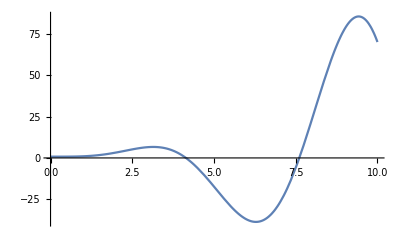

```mathematica
Plot[res[x],{x,0,10}]
```

# The END.